# Large N Sachdev-Ye-Kitaev model

## Example of working with Fourier transforms and iterative algorithms.

```mathematica
SetDirectory@NotebookDirectory[];
```

## Schwinger-Dyson equation solver

The phase change defined below is necessary due to Mathematica’s Fourier/InverseFourier conventions.
One needs to find it by hand, and there is some ambiguity related to the choice of Euclidean-time discretization.
In this case we choose to discretize τ∈[0,β) using τ_j=β/(2K)(j-1) with for j=1,2,...

```mathematica
ClearAll@SDSolve;
SDSolve[k_Integer,α_Real,ϵ_Real][β_Real]:=
Block[{phase=β Table[(-1)^(j-1)ⅇ^(ⅈ π(j-1)/(2k)),{j,2k}],fourier,invfourier,ωs,G,Gt,S,St,dist,cur=1},
invfourier=phase^-1 InverseFourier[#,FourierParameters->{-1, 1}]&;
fourier=Fourier[# phase,FourierParameters->{-1, 1}]&;
ωs=(2π)/β(Range[-k+1,k]-1/2);
Gt[0]=(-ⅈ ωs)^-1;
G[n_]:=G[n]=invfourier@Gt[n];
S[n_]:=S[n]=G[n]^3;
St[n_]:=St[n]=fourier@S[n];
Gt[n_]:=Gt[n]=(1-α)Gt[n-1]+α(-ⅈ ωs-St[n-1])^-1;
dist[n_]:=dist[n]=Mean@Abs[Gt[n]-Gt[n-1]];
While[dist[cur]>ϵ,cur++];
Gt[cur]
]
```

### Plots

In order to plot the solutions in Euclidean-time, it is convenient to add and subtract the free-fermion solution to avoid Fourier-transforming discontinuous functions

```mathematica
ClearAll@PlotSolution;
PlotSolution[k_Integer,α_Real,ϵ_Real][β_Real][color_]:=
Block[{phase=β Table[(-1)^(j-1)ⅇ^(ⅈ π(j-1)/(2k)),{j,2k}],fourier,invfourier,ts,ωs},
invfourier=phase^-1 InverseFourier[#,FourierParameters->{-1, 1}]&;
fourier=Fourier[# phase,FourierParameters->{-1, 1}]&;
ωs=(2π)/β(Range[-k+1,k]-1/2);
ts=β/(2k)Range[0,2k-1];
ListPlot[Transpose@{ts/β,invfourier[SDSolve[k,α,ϵ][β]-(-ⅈ ωs)^-1]+1/2},Joined->True,PlotRange->All,AxesLabel->{"τ/β","G(τ)"},AxesStyle->Black,TicksStyle->Medium,ImageSize->1024,PlotStyle->color,PlotLegends->LineLegend[{color},{"β = "<>ToString@β}],AxesStyle->Black,TicksStyle->Medium]
]
```

```mathematica
Show[{
PlotSolution[2^16,.5,10.^-9][5.][Blue],
PlotSolution[2^16,.5,10.^-9][10.][Orange],
PlotSolution[2^16,.5,10.^-9][100.][Red]
},PlotRange->{0,.5},AxesOrigin->{0,0}
]
```

-Graphics-

```mathematica
Export["SolutionExample.pdf",%]
```

SolutionExample.pdf

## Thermodynamics

Computing the entropy is straightforward...

```mathematica
SYKEntropy[k_Integer,α_Real,ϵ_Real][β_Real]:=
Block[{ωs,Gt=SDSolve[k,α,ϵ][β]},
ωs=(2π)/β(Range[-k+1,k]-1/2);
1/2 Log@2-Sum[Log@Abs[-ⅈ ωs⟦i⟧Gt⟦i⟧]+5/4(1-Re[-ⅈ ωs⟦i⟧Gt⟦i⟧]),{i,k+1,2k}]
]
```

We can extrapolate linearly to T→0, finding good agreement

```mathematica
LinearModelFit[Table[{β^-1,SYKEntropy[2^16,.5,10.^-9][β]},{β,{100.,110.}}],T,T][0]
```

0.23115

```mathematica
Catalan/(2π)+(Log@2)/8//N
```

0.232424

When computing thermodynamic functions, one should be careful about truncation errors becoming very important at low-temperatures...

```mathematica
SYKEntropy[2^16,.1,10.^-9][200.]
```

0.233133

```mathematica
SYKEntropy[2^16,.1,10.^-9][500.]
```

0.223567

```mathematica
SYKEntropy[2^16,.1,10.^-9][1000.]
```

0.19395

## Optional parts

### A solver with arbitrary starting point and a mass term

```mathematica
ClearAll@SDSolve2;
SDSolve2[k_Integer,α_Real,ϵ_Real,Gt0_][m_Real,β_Real]:=
Block[{phase=β Table[(-1)^(j-1)ⅇ^(ⅈ π(j-1)/(2k)),{j,2k}],fourier,invfourier,ωs,G,Gt,S,St,dist,cur=1},
invfourier=phase^-1 InverseFourier[#,FourierParameters->{-1, 1}]&;
fourier=Fourier[# phase,FourierParameters->{-1, 1}]&;
ωs=(2π)/β(Range[-k+1,k]-1/2);
Gt[0]=Gt0;
G[n_]:=G[n]=invfourier@Gt[n];
S[n_]:=S[n]=G[n]^2 Reverse@G[n];(* ugly but should work! *)
(*S[n_]:=S[n]=-G[n]^2Prepend[Reverse@G[n]⟦2;;⟧,First@G[n]];*)
St[n_]:=St[n]=fourier@S[n];
Gt[n_]:=Gt[n]=(1-α)Gt[n-1]+α(m-ⅈ ωs-St[n-1])^-1;
dist[n_]:=dist[n]=Mean@Abs[Gt[n]-Gt[n-1]];
While[dist[cur]>ϵ,cur++];
Gt[cur]
]
```

#### The high-temperature starting point

```mathematica
ClearAll@TreeLevelStart;
TreeLevelStart[k_Integer][m_Real,β_Real]:=With[{ωs=(2π)/β(Range[-k+1,k]-1/2)},(m-ⅈ ωs)^-1];
```

### Non-vanishing-mass solutions are asymmetric

```mathematica
ClearAll@PlotSolution3;
PlotSolution3[m_Real,β_Real][Gt_][color_]:=
Block[{k=1/2 Length@Gt,Gt0,phase,fourier,invfourier,ts},
phase=β Table[(-1)^(j-1)ⅇ^(ⅈ π(j-1)/(2k)),{j,2k}];
invfourier=phase^-1 InverseFourier[#,FourierParameters->{-1, 1}]&;
fourier=Fourier[# phase,FourierParameters->{-1, 1}]&;
Gt0=TreeLevelStart[k][m,β];
ts=β/(2k)Range[0,2k-1];
ListPlot[Transpose@{ts/β,invfourier[Gt-Gt0]+ⅇ^(m(β-ts))/(ⅇ^(β m)+1)},Joined->True,PlotRange->All,AxesLabel->{"τ/β","G(τ)"},AxesStyle->Black,TicksStyle->Medium,ImageSize->1024,PlotStyle->color,PlotLegends->LineLegend[{color},{"β = "<>ToString@β}],AxesStyle->Black,TicksStyle->Medium]
]
```

```mathematica
With[{k=2^14,m=0.1,β=20.},
SDSolve2[k,.25,10.^-9,TreeLevelStart[k][m,β]][m,β];
]
```

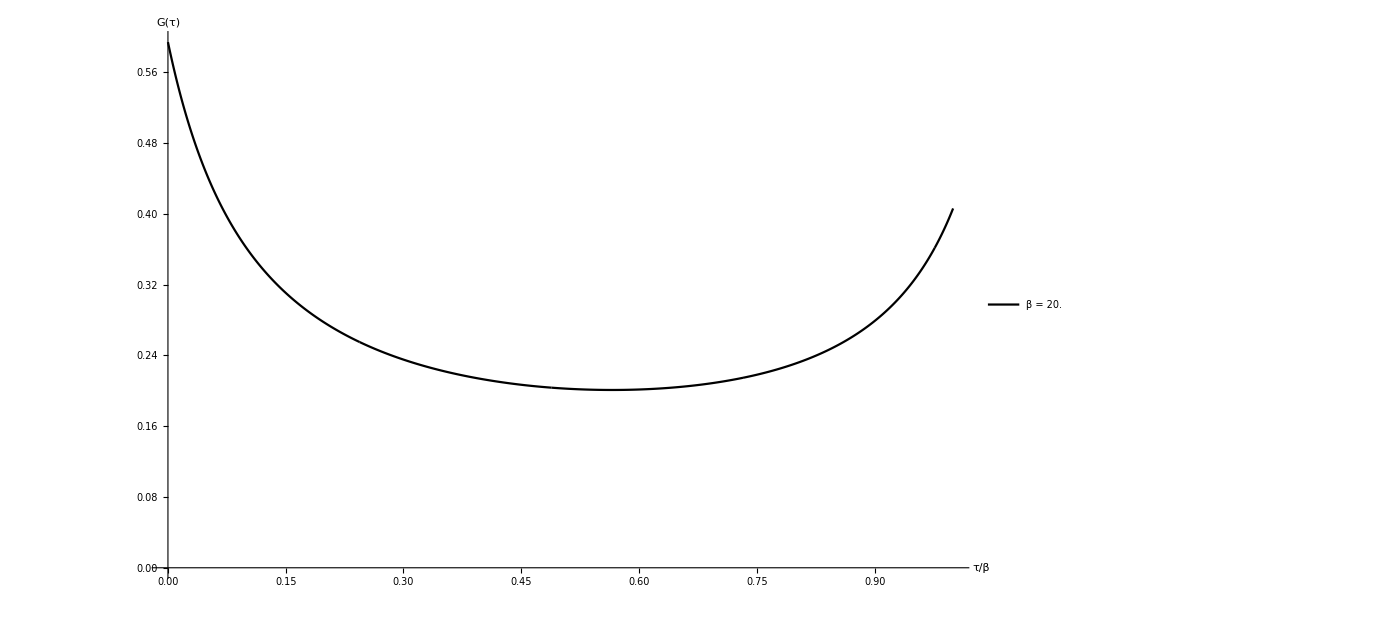

```mathematica
PlotSolution3[.1,20.][%][Black]
```

### Thermodynamics

```mathematica
ClearAll@SYKEntropy2;
SYKEntropy2[m_Real,β_Real][Gt_]:=
Block[{k=1/2 Length@Gt,Gt0},
Gt0=TreeLevelStart[k][m,β];
Log[1+ⅇ^(β m)]-(β m)/(ⅇ^(-β m)+1)-Sum[2m Re[Gt⟦i⟧-Gt0⟦i⟧]+2Log@Abs[Gt⟦i⟧/Gt0⟦i⟧]+5/2(1-Re[Gt⟦i⟧/Gt0⟦i⟧]),{i,k+1,2k}]
]
```

```mathematica
With[{k=2^14,m=0.,β=20.},
SDSolve2[k,.25,10.^-9,TreeLevelStart[k][m,β]][m,β];
]
```

```mathematica
SYKEntropy2[0.,20.][%]
```

0.501873

```mathematica
2SYKEntropy[2^16,.25,10.^-9][20.]
```

0.501698

```mathematica
Dynamic@{m,cur,dist[cur]}
```

```mathematica
IncMassData=Block[{k=2^14,β=20.,sol},
sol=TreeLevelStart[k][0.,β];
Table[
sol=SDSolve2[k,.25,10.^-9,sol][m,β];
{m,SYKEntropy2[m,β][sol]}
,{m,0.,.6,.01}]
]
```

{{0.,0.501873},{0.01,0.501711},{0.02,0.501387},{0.03,0.500849},{0.04,0.500094},{0.05,0.499118},{0.06,0.497919},{0.07,0.49649},{0.08,0.494827},{0.09,0.492922},{0.1,0.490766},{0.11,0.48835},{0.12,0.48566},{0.13,0.482685},{0.14,0.479406},{0.15,0.475805},{0.16,0.471859},{0.17,0.46754},{0.18,0.462817},{0.19,0.457651},{0.2,0.451991},{0.21,0.44578},{0.22,0.438942},{0.23,0.431378},{0.24,0.422958},{0.25,0.413505},{0.26,0.402762},{0.27,0.390336},{0.28,0.375574},{0.29,0.357227},{0.3,0.332222},{0.31,0.284309},{0.32,0.0170747},{0.33,0.0133891},{0.34,0.0106826},{0.35,0.00862234},{0.36,0.00701834},{0.37,0.00574888},{0.38,0.00473007},{0.39,0.00390821},{0.4,0.00323713},{0.41,0.00268769},{0.42,0.00223596},{0.43,0.00186337},{0.44,0.00155529},{0.45,0.00130274},{0.46,0.00109096},{0.47,0.000915044},{0.48,0.000768791},{0.49,0.000647123},{0.5,0.000545861},{0.51,0.000461556},{0.52,0.000391354},{0.53,0.000332891},{0.54,0.000284201},{0.55,0.000243653},{0.56,0.000209887},{0.57,0.000181772},{0.58,0.000158365},{0.59,0.000142413},{0.6,0.000126199}}

```mathematica
DecMassData=Block[{k=2^14,β=20.,sol},
sol=TreeLevelStart[k][0.,β];
Table[
sol=SDSolve2[k,.25,10.^-9,sol][m,β];
{m,SYKEntropy2[m,β][sol]}
,{m,.6,0.,-.01}]
]
```

{{0.6,0.000117522},{0.59,0.00011418},{0.58,0.000133648},{0.57,0.000160582},{0.56,0.000188693},{0.55,0.000222454},{0.54,0.000262995},{0.53,0.000311676},{0.52,0.000370129},{0.51,0.000440318},{0.5,0.000524608},{0.49,0.000625851},{0.48,0.000747495},{0.47,0.000893716},{0.46,0.00106959},{0.45,0.00128132},{0.44,0.00153918},{0.43,0.00184718},{0.42,0.00221967},{0.41,0.00267126},{0.4,0.0032205},{0.39,0.00389127},{0.38,0.00471696},{0.37,0.00573516},{0.36,0.00700536},{0.35,0.00861105},{0.34,0.0106715},{0.33,0.0133793},{0.32,0.0170645},{0.31,0.0223734},{0.3,0.0309294},{0.29,0.0509469},{0.28,0.375579},{0.27,0.390342},{0.26,0.402768},{0.25,0.413511},{0.24,0.422964},{0.23,0.431382},{0.22,0.438945},{0.21,0.445783},{0.2,0.451994},{0.19,0.457652},{0.18,0.462819},{0.17,0.467541},{0.16,0.471859},{0.15,0.475805},{0.14,0.479406},{0.13,0.482684},{0.12,0.48566},{0.11,0.488349},{0.1,0.490766},{0.09,0.492922},{0.08,0.494827},{0.07,0.49649},{0.06,0.497918},{0.05,0.499118},{0.04,0.500093},{0.03,0.500849},{0.02,0.501387},{0.01,0.50171},{0.,0.50182}}

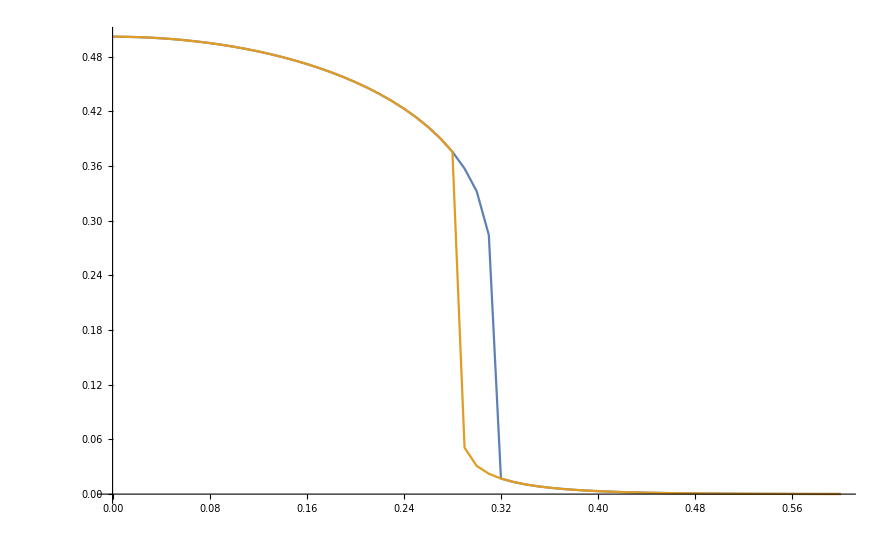

```mathematica
ListPlot[{IncMassData,DecMassData},Joined->True]
```